```mathematica
Off[ClebschGordan::"tri"]
Off[ClebschGordan::"phy"]
Off[General::"spell1"]
Off[General::"spell"]
Off[Graphics::"gprim"]
Off[Set::"wrsym"]
δ[n1_,n2_]:=KroneckerDelta[n1,n2];
<<"ErrorBarPlots`"
timesfont[x_]:=BaseStyle->{FontFamily->"Times",FontSize->x};
SetOptions[ListPlot,PlotStyle->{Red,Green,Blue,Purple,Black},Joined->True,PlotRange->All,Frame->True,Axes->False,ImageSize->500,timesfont[20]];
SetOptions[Plot,PlotStyle->{Red,Green,Blue,Purple,Black},PlotRange->All,Frame->True,Axes->False,ImageSize->350,timesfont[20]];
SetOptions[ListLogLinearPlot,PlotStyle->{Red,Green,Blue,Purple,Black},Joined->True,PlotRange->All,Frame->True,Axes->False];
datapoint[len_,th_]:={Graphics[{Evaluate[Thickness[th/len]],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]}],len/20};
DFOff:=DisplayFunction->Identity;
DFOn:=DisplayFunction->$DisplayFunction;
Gs[size_]:={ImageSize->size};
(*NN[x_,m_]:=SetPrecision[x,m];*)
Dim[x_]:=Dimensions[x];
readAgilent[fname_]:=Module[{stream,header,n},stream=OpenRead[fname];header=ReadList[stream,String,2];n=Which[header⟦1⟧=="x-axis,RB3",2,header⟦1⟧=="x-axis,1",2,header⟦1⟧=="x-axis,2",2,header⟦1⟧=="x-axis,1,2",3,header⟦1⟧=="x-axis,1,2,MATH",4];Partition[ReadList[stream,Number,RecordSeparators->{","}],n]];
readTektronix[fname_]:=ToExpression[Module[{stream,header},stream=OpenRead[fname];header=ReadList[stream,String,18];Partition[ReadList[stream,Record,RecordSeparators->{",","\n"},NullRecords->False],2]]];
readdat[fname_,numcols_,headlines_,recsep_]:=Module[{stream,header},stream=OpenRead[fname];header=ReadList[stream,String,headlines];Partition[ReadList[stream,Number,RecordSeparators->{recsep,"\n"}],numcols]];
Needs["PlotLegends`"]
```

```mathematica
k=8.99*^9;
ee=1.6*^-19;
m=9.11*^-31;
Ex=-3*^6;
Ey=0;
v0=290188.37643213599829660469770936;
```

```mathematica
sols=NDSolve[{x'[t]==vx[t],vx'[t]==-(k ee^2 x[t])/(m (x[t]^2+y[t]^2)^(3/2))-(ee Ex)/m,y'[t]==vy[t],vy'[t]==-(k ee^2 y[t])/(m (x[t]^2+y[t]^2)^(3/2))-(ee Ey)/m,x[0]==3*^-9,y[0]==0,vx[0]==0,vy[0]==v0},{x,vx,y,vy},{t,0,1*^-12}];
```

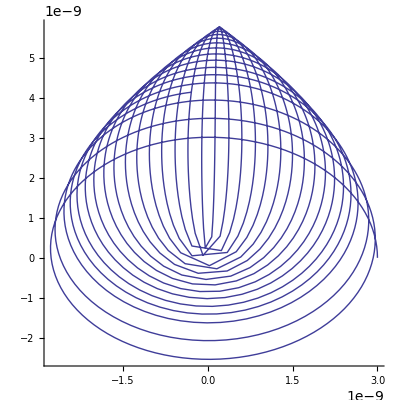

```mathematica
data=Flatten[Table[{x[t],y[t]}/.sols,{t,0,1*^-12,5*^-16}],1];
ListPlot[data,Joined->True,AspectRatio->1]
```

```mathematica
Solve[(k ee^2)/((3*^-9)^2)==(m v^2)/(3*^-9),v]
```

{{v→-290188.},{v→290188.}}

```mathematica
{x[t],y[t]}/.sols
```

{{InterpolatingFunction[{{0.,3.×10^-7}},<>][t],InterpolatingFunction[{{0.,3.×10^-7}},<>][t]}}

```mathematica
num=16320;
h0=5*^-16;

k=8.99*^9;
ee=1.6*^-19;
m=9.11*^-31;
Ex=-3*^6;
Ey=0;

t=Table[0,{num}];
h=t;
x=t;
y=t;
vx=t;
vy=t;
h⟦1⟧=h0;
x⟦1⟧=3*^-9;
y⟦1⟧=0;
vx⟦1⟧=0;
vy⟦1⟧=290188.37643213599829660469770936;
Do[

h⟦n⟧=(x⟦n-1⟧^2+y⟦n-1⟧^2)/(x⟦1⟧^2+y⟦1⟧^2) h0;

t⟦n⟧=t⟦n-1⟧+h⟦n⟧;

p1=vx⟦n-1⟧;
q1=vy⟦n-1⟧;
r1=-(k ee^2 x⟦n-1⟧)/(m (x⟦n-1⟧^2+y⟦n-1⟧^2)^(3/2))-(ee Ex)/m;
s1=-(k ee^2 y⟦n-1⟧)/(m (x⟦n-1⟧^2+y⟦n-1⟧^2)^(3/2))-(ee Ey)/m;

p2=vx⟦n-1⟧+h⟦n⟧/2*r1;
q2=vy⟦n-1⟧+h⟦n⟧/2*s1;
r2=-(k ee^2 (x⟦n-1⟧+h⟦n⟧/2*p1))/(m ((x⟦n-1⟧+h⟦n⟧/2*p1)^2+(y⟦n-1⟧+h⟦n⟧/2*q1)^2)^(3/2))-(ee Ex)/m;
s2=-(k ee^2 (y⟦n-1⟧+h⟦n⟧/2*q1))/(m ((x⟦n-1⟧+h⟦n⟧/2*p1)^2+(y⟦n-1⟧+h⟦n⟧/2*q1)^2)^(3/2))-(ee Ey)/m;

p3=vx⟦n-1⟧+h⟦n⟧/2*r2;
q3=vy⟦n-1⟧+h⟦n⟧/2*s2;
r3=-(k ee^2 (x⟦n-1⟧+h⟦n⟧/2*p2))/(m ((x⟦n-1⟧+h⟦n⟧/2*p2)^2+(y⟦n-1⟧+h⟦n⟧/2*q2)^2)^(3/2))-(ee Ex)/m;
s3=-(k ee^2 (y⟦n-1⟧+h⟦n⟧/2*q2))/(m ((x⟦n-1⟧+h⟦n⟧/2*p2)^2+(y⟦n-1⟧+h⟦n⟧/2*q2)^2)^(3/2))-(ee Ey)/m;

p4=vx⟦n-1⟧+h⟦n⟧*r3;
q4=vy⟦n-1⟧+h⟦n⟧*s3;
r4=-(k ee^2 (x⟦n-1⟧+h⟦n⟧*p3))/(m ((x⟦n-1⟧+h⟦n⟧*p3)^2+(y⟦n-1⟧+h⟦n⟧*q3)^2)^(3/2))-(ee Ex)/m;
s4=-(k ee^2 (y⟦n-1⟧+h⟦n⟧*q3))/(m ((x⟦n-1⟧+h⟦n⟧*p3)^2+(y⟦n-1⟧+h⟦n⟧*q3)^2)^(3/2))-(ee Ey)/m;

x⟦n⟧=x⟦n-1⟧+h⟦n⟧/6*(p1+2 p2+2 p3+p4);
y⟦n⟧=y⟦n-1⟧+h⟦n⟧/6*(q1+2 q2+2 q3+q4);
vx⟦n⟧=vx⟦n-1⟧+h⟦n⟧/6*(r1+2 r2+2 r3+r4);
vy⟦n⟧=vy⟦n-1⟧+h⟦n⟧/6*(s1+2 s2+2 s3+s4);

,{n,2,num}]
```

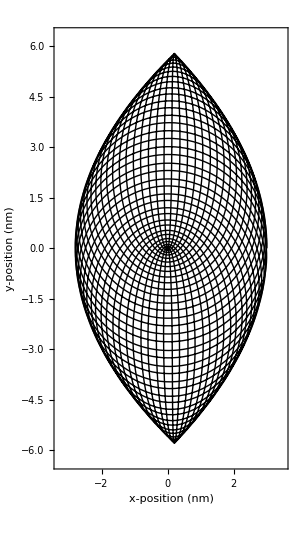

```mathematica
ListPlot[Transpose[{1*^9*x,1*^9*y}],Frame->True,Axes->False,Joined->True,ImageSize->300,AspectRatio->Automatic,PlotRange->{{-3.3,3.5},{-6.3,6.3}},PlotStyle->Black,FrameLabel->{"x-position (nm)","y-position (nm)"}]
```

```mathematica
rydfnx=Interpolation[Transpose[{1*^15*t,1*^9*x}]];
rydfny=Interpolation[Transpose[{1*^15*t,1*^9*y}]];
```

```mathematica
xeven=Table[rydfnx[t],{t,0,2342,0.05}];
yeven=Table[rydfny[t],{t,0,2342,0.05}];
```

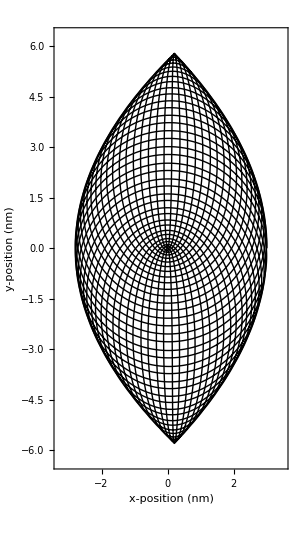

```mathematica
ListPlot[Transpose[{xeven,yeven}],Frame->True,Axes->False,Joined->True,ImageSize->300,AspectRatio->Automatic,PlotRange->{{-3.3,3.5},{-6.3,6.3}},PlotStyle->Black,FrameLabel->{"x-position (nm)","y-position (nm)"}]
```

```mathematica
mov=Table[ListPlot[Transpose[{xeven⟦1;;q⟧,yeven⟦1;;q⟧}],Frame->True,Axes->False,Joined->True,ImageSize->300,AspectRatio->Automatic,PlotRange->{{-3.3,3.5},{-6.3,6.3}},PlotStyle->Black,FrameLabel->{"x-position (nm)","y-position (nm)"}],{q,1,Length[xeven],100}];
```

```mathematica
SetDirectory["C:\\Documents and Settings\\April Steele\\My Documents\\Jeff's\\Physics"];
Export["RydMovie.gif",mov];
```

```mathematica
Length[xeven]/100.
```

468.41

```mathematica
T=0;
list={};
Do[If[t⟦n⟧≥T,
list=Join[list,{n}];
T=T+h0;
];
,{n,num}]
```

```mathematica
N[t⟦-1⟧/h0]
```

4685.08

```mathematica
Length[list]
```

4684

```mathematica
list⟦1;;100⟧
```

{2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,56,57,58,59,60,61,62,63,64,65,67,68,69,70,71,72,74,75,76,77,79,80,81,83,84,85,86,88,89,91,92,93,95,96,97,99,100,102,103,104,106,107,109,110,111,113,114}

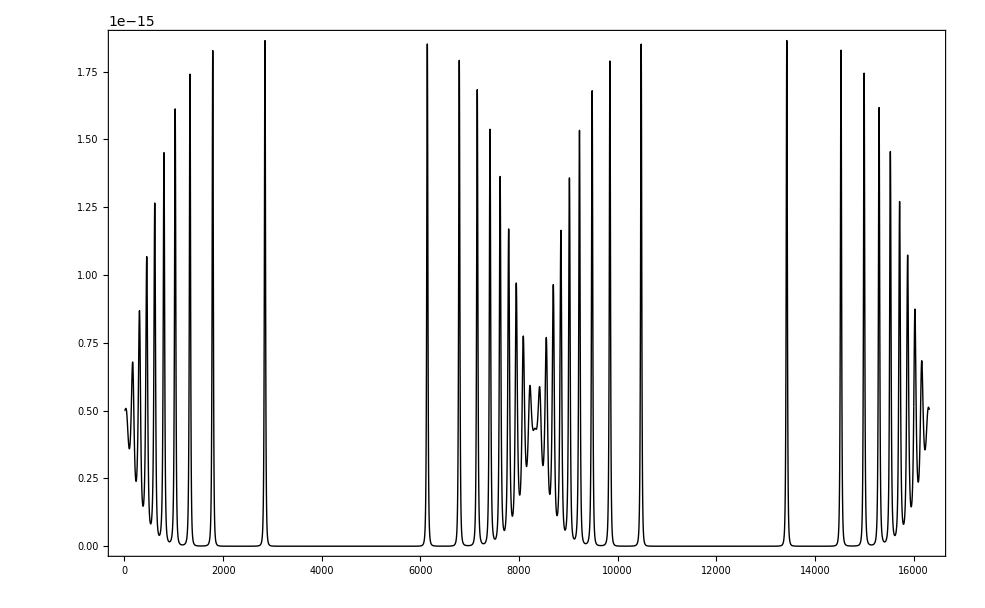

```mathematica
ListPlot[h]
```

```mathematica
Min[h]
```

3.03821×10^-22

```mathematica
Table[1,{6}]
```

{1,1,1,1,1,1}

```mathematica
Solve[(k ee^2)/((3*^-9)^2)==(m v^2)/(3*^-9),v]
```

{{v→-290188.},{v→290188.}}